```mathematica
Emaad Khwaja-Forward Euler and Backward Euler-Math 385-05/09/16
```

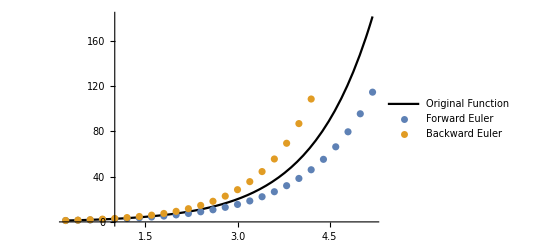

```mathematica
f[x_]:=E^x;
Δx=.2;
Subscript[a, 0]=1;
Subscript[b, 0]=1;
Subscript[a, 1]=Subscript[a, 0];
Subscript[b, 1]=Subscript[b, 0];
A={};
B={};

(*Forward Euler*)

While[Subscript[a, 0]<100,
Subscript[a, 1]=Subscript[a, 0]+Subscript[a, 0]*Δx;
Subscript[a, 0]=Subscript[a, 1];
AppendTo[A,Subscript[a, 0]];
]


(*Backward Euler*)
While[Subscript[b, 0]<100,
Subscript[b, 1]=Subscript[b, 0]/(1-Δx);
Subscript[b, 0]=Subscript[b, 1];
AppendTo[B,Subscript[b, 0]];
]

Subscript[A, 1]=Δx*Range[Length[A]];
Subscript[A, 2]=Transpose[{Subscript[A, 1],A}];
Subscript[B, 1]=Δx*Range[Length[B]];
Subscript[B, 2]=Transpose[{Subscript[B, 1],B}];

Show[
Plot[f[x],{x,Min[Subscript[B, 1]],Max[Subscript[A, 1]]},PlotLegends->LineLegend[{"Original Function"}],PlotStyle->Black],
ListPlot[{Subscript[A, 2],Subscript[B, 2]},PlotLegends->{"Forward Euler", "Backward Euler"}]
]
```